```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\flux_pmf\xin\PVP5\100Ag\push_into_surface\k_1.7\60_windows_us\2_IC_stampede\1.5ns\k_1.7\ui_nostat

```mathematica
log=OpenRead["fe_ui.xy"];
Find[log," # Reaction coordinate"];
pmfUI=ReadList[log,{Number,Number}];
Close[log];
```

```mathematica
log=OpenRead["fe_wham.xy"];
Find[log," # Reaction coordinate"];
pmfWHAM=ReadList[log,{Number,Number}];
Close[log];
```

```mathematica
log=OpenRead["global_histogram.xy"];
Find[log," # Reaction coord"];
dataHist=ReadList[log,{Number,Number}];
Close[log];
```

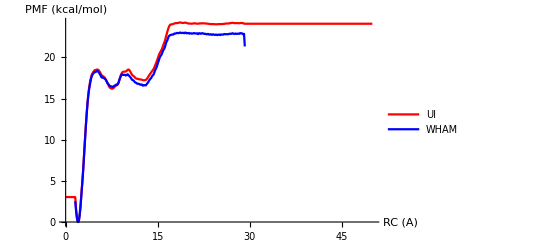

```mathematica
GraphPMF=ListLinePlot[{pmfUI,pmfWHAM},AxesLabel->{"RC (A)","PMF (kcal/mol)"},LabelStyle->Directive[FontSize->15],PlotStyle->{Red,Blue},PlotRange->{{0,50},All},PlotLegends->{"UI","WHAM"}]
```

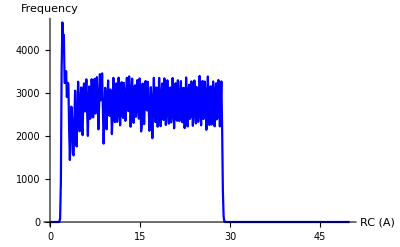

```mathematica
GraphHist=ListLinePlot[dataHist,AxesLabel->{"RC (A)","Frequency"},LabelStyle->Directive[FontSize->15],PlotStyle->Blue,PlotRange->{{0,50},All}]
```

```mathematica
CreateDirectory["graphs"];
Export["graphs/PMF.png",GraphPMF,ImageResolution->100];
Export["graphs/Histogram.png",GraphHist,ImageResolution->100];
```

CreateDirectory::filex: "D:\\tonnam_backup\\Research_scratch\\flux_pmf\\xin\\PVP5\\100Ag\\push_into_surface\\k_1.7\\60_windows_us\\2_IC_stampede\\1.5ns\\k_1.7\\ui_nostat\\graphs\\" already exists.

```mathematica
pmfUI0=pmfUI;
pmfWHAM0=pmfWHAM;
```

```mathematica
pmfUI0[[All,2]]=pmfUI[[All,2]]-pmfUI[[-1,2]];
pmfWHAM0[[All,2]]=pmfWHAM[[All,2]]-pmfWHAM[[-4,2]];
```

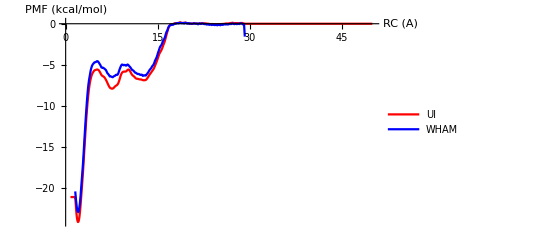

```mathematica
GraphPMF0=ListLinePlot[{pmfUI0[[30;;-1]],pmfWHAM0},AxesLabel->{"RC (A)","PMF (kcal/mol)"},LabelStyle->Directive[FontSize->15],PlotStyle->{Red,Blue},PlotRange->{{0,50},All},PlotLegends->{"UI","WHAM"}]
```

```mathematica
Export["graphs/PMF0.png",GraphPMF0,ImageResolution->100];
```